# Circuit Diagram

"Diagram" is a property of QuantumCircuitOperator, with some options for customizing that. Here we shall briefly review those options.

"ShowWires" | True | whether to show horizontal wires
"WireLabels" | Automatic | wire labeling
"MeasurementWireLabel" | "c" | measurement wire label
"MeasurementWirePosition" | Top | measurement wire position
"ShowMeasurementWire" | True | whether to show a measurement wire
"ShowEmptyWires" | True | whether to render empty wires
"ShowExtraQudits" | False | whether to show non-positive ancillas

Wires.

"ShowLabel" | False | whether to include a circuit label
"ShowGateLabels" | True | whether to show labels on gates
"RotateGateLabel" | Automatic | rotation angle of gate labels
"IdentityGate" | False | where to show Identity gate

Labels.

"Size" | .75 | operator size
"HorizontalGapSize" | 1 | distance between operators
"VerticalGapSize" | 1 | distance between wires

Sizes.

"GateBackgroundStyle" | Automatic | gate background style rules
"GateBoundaryStyle" | Automatic | gate boundary style rules
"GateShapeFunction" | Automatic | custom function to render gates

Styling.

"ShowOutline" | False | outline a circuit with a frame
"ShowConnectors" | False | show points of wire-gate connections
"ShowWireEndpoints" | False | show wire end-points

Various graphics elements.

"Expand" | 1 | level of subcircuits to expand up-to
"SubcircuitOptions" | {} | pass additional diagram options to subcircuits

Sub-circuits.

Barriers can be added to shift gate positions:

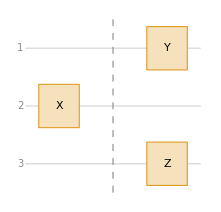

```mathematica
QuantumCircuitOperator[{"X"->2,"Barrier"[;;3],"Y"->1,"Z"->3}]["Diagram"]
```

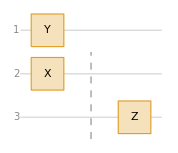

```mathematica
QuantumCircuitOperator[{"X"->2,"Barrier"[2;;],"Y"->1,"Z"->3}]["Diagram"]
```

"GateBackgroundStyle" and "GateBoundaryStyle" can include rules for changing gate appearance:

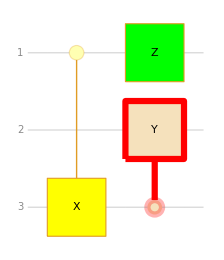

```mathematica
QuantumCircuitOperator[{"CX"->{1,3},"CY"->{3,2},"Z"}]["Diagram","GateBackgroundStyle"->{"X"->Yellow,"Z"->Green},"GateBoundaryStyle"->{"Y"->Directive[Thickness[0.02],Red]}]
```

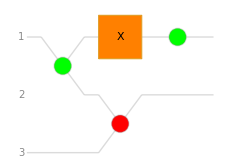

```mathematica
QuantumCircuitOperator[{"ZSpider"->1->{1,2},"XSpider"->{2,3}->2,"X","ZSpider"}]["Diagram","GateBackgroundStyle"->{"ZSpider"->Green,"XSpider"->Red,"X"->Orange}]
```

"GateShapeFunction" can be specified to render gates with a custom function that takes {center, label, horizontalPositions, verticalPositions} arguments:

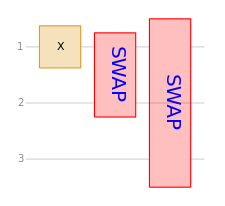

```mathematica
QuantumCircuitOperator[{"X","SWAP","SWAP"->{1,3}}]["Diagram","GateShapeFunction"->"SWAP"->Function[{center,label,hPos,vPos},{EdgeForm[Red],FaceForm[Directive[Red,Opacity[0.25]]],Rectangle[center-{.375,.75(Max[vPos]-Min[vPos])},center+{.375,.75(Max[vPos]-Min[vPos])},RoundingRadius->0.1],Text[Style[Rotate[label,-Pi/2],20,Blue],center]}]
]
```

"Size", "HorizontalGapSize" and "VerticalGapSize" correspondingly control gate size, distance between gates and a distance between wires:

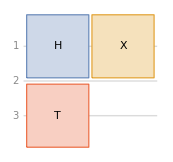

```mathematica
QuantumCircuitOperator[{"H","X","T"->{3}}]["Diagram","Size"->.5,"VerticalGapSize"->.275,"HorizontalGapSize"->.525]
```

"ShowConnectors" → True shows connection points of wires with gates:

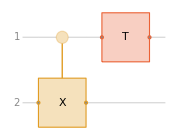

```mathematica
QuantumCircuitOperator[{"CX","T"}]["Diagram","ShowConnectors"->True]
```

"ShowEmptyWires" → False removes wires without any gates from a diagram:

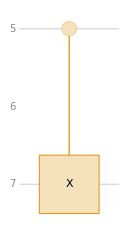

```mathematica
QuantumCircuitOperator[{"CX"->{5,7}}]["Diagram","ShowEmptyWires"->False]
```

"ShowOutline" → True shows a frame outlining a circuit:

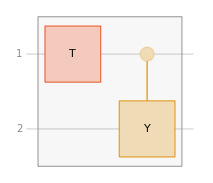

```mathematica
QuantumCircuitOperator[{"T","CY"}]["Diagram","ShowOutline"->True]
```

"Expand" specifies a level depth of sub-circuits to expand:

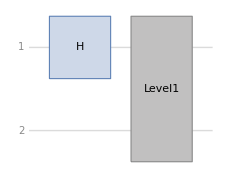

```mathematica
QuantumCircuitOperator[{"H",QuantumCircuitOperator[{"T",QuantumCircuitOperator[{"CX","H"},"Level2"],"H"},"Level1"]}]["Diagram","Expand"->0]
```

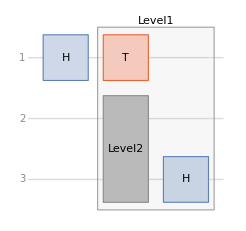

```mathematica
QuantumCircuitOperator[{"H",QuantumCircuitOperator[{"T",QuantumCircuitOperator[{"CX"->{2,3},"H"->2},"Level2"],"H"->3},"Level1"]}]["Diagram","Expand"->1]
```

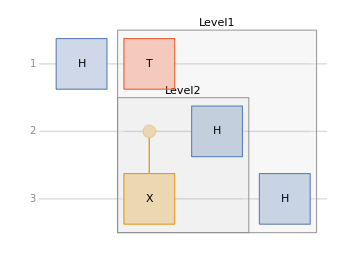

```mathematica
QuantumCircuitOperator[{"H",QuantumCircuitOperator[{"T",QuantumCircuitOperator[{"CX"->{2,3},"H"->2},"Level2"],"H"->3},"Level1"]}]["Diagram","Expand"->2]
```

"Expand" can be specified explicitly as an option to any sub-circuit:

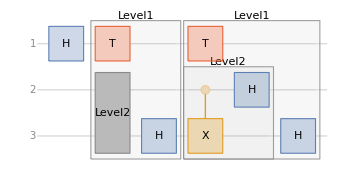

```mathematica
QuantumCircuitOperator[{"H",QuantumCircuitOperator[{"T",QuantumCircuitOperator[{"CX"->{2,3},"H"->2},"Level2","Expand"->False],"H"->3},"Level1"],
QuantumCircuitOperator[{"T",QuantumCircuitOperator[{"CX"->{2,3},"H"->2},"Level2"],"H"->3},"Level1"]}]["Diagram","Expand"->2]
```

"SubcircuitOptions" can be used to pass options to all sub-circuit diagrams:

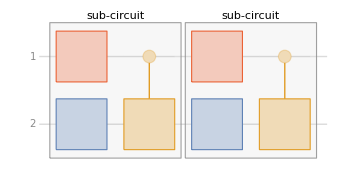

```mathematica
QuantumCircuitOperator[{QuantumCircuitOperator[{"T","H"->{2},"CX"},Style["sub-circuit",Background->White]],QuantumCircuitOperator[{"T","H"->{2},"CX"},Style["sub-circuit",Background->White]]}]["Diagram","SubcircuitOptions"->{"ShowGateLabels"->False}]
```

Or pass options directly to individual sub-circuits:

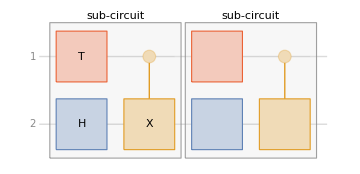

```mathematica
QuantumCircuitOperator[{QuantumCircuitOperator[{"T","H"->{2},"CX"},Style["sub-circuit",Background->White],"ShowGateLabels"->True],QuantumCircuitOperator[{"T","H"->{2},"CX"},Style["sub-circuit",Background->White],"ShowGateLabels"->False]}]["Diagram"]
```

"ShowMeasurementWire" → False hides a measurement wire:

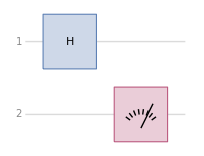

```mathematica
QuantumCircuitOperator[{"H",{2}}]["Diagram","ShowMeasurementWire"->False]
```

"MeasurementWirePosition" can be Top or Bottom:

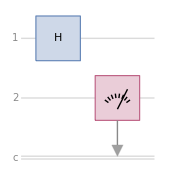

```mathematica
QuantumCircuitOperator[{"H",{2}}]["Diagram","MeasurementWirePosition"->Bottom]
```

Show extra qudits used by channels and measurements:

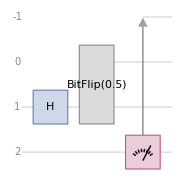

```mathematica
QuantumCircuitOperator[{"H","BitFlip",{2}}]["Diagram","ShowExtraQudits"->True]
```

Extra qudits are always shown when there is an explicit gate there:

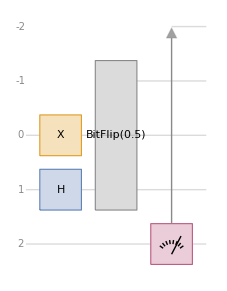

```mathematica
QuantumCircuitOperator[{"H","X"->0,"BitFlip",{2}}]["Diagram"]
```

"WireLabels" can be a list of labels or a list of rules:

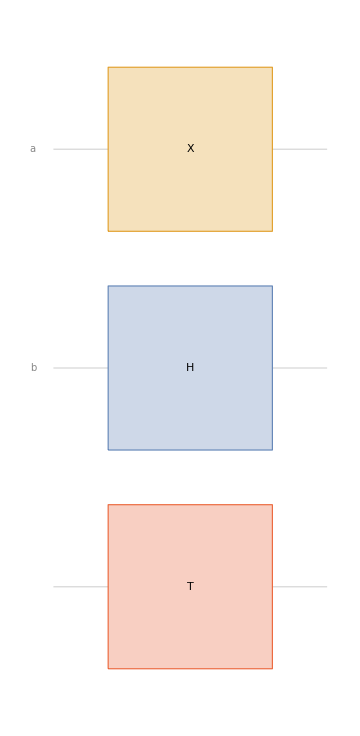
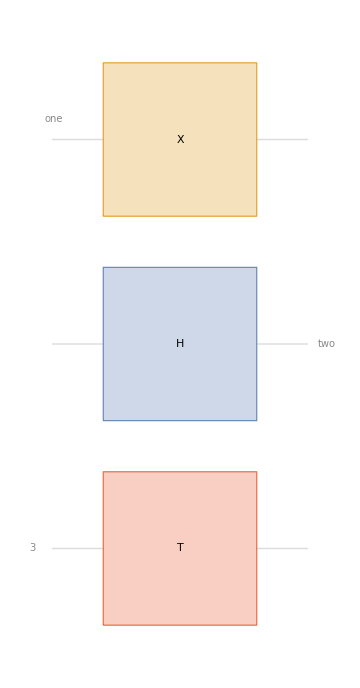

```mathematica
Row[{QuantumCircuitOperator[{"X","H"->{2},"T"->{3}}]["Diagram","WireLabels"->{a,b}],
QuantumCircuitOperator[{"X","H"->{2},"T"->{3}}]["Diagram","WireLabels"->{2->Placed["two",Right],1->Placed["one",{0,.1}]}]
}]
```

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFramework`

Wolfram/QuantumFramework/tutorial/CircuitDiagram

### Keywords

Quantum circuit